```mathematica
(* Question 1 a*)
For[m=1;n=15;r=7;i=0,i<r,i++,m=m*(n-i)/(r-i)]
m
n=15;
r=7;
i=0;
k=1;
While[i<r,k=k*(n-i)/(r-i);i++]
k
```

6435

6435

```mathematica
(* Qusetion 1 b*)
A={1,2,3,4,5,7};
B={2,4,6,8,9};
A∩B
Intersection[B,A]
```

{2,4}

{2,4}

```mathematica
(* question 1 c*)
lhs=LogicalExpand[¬(p∨q)];
rhs=LogicalExpand[¬p∧¬q];
lhs==rhs
lhs=LogicalExpand[¬(p∧q)];
rhs=LogicalExpand[¬p∨¬q];
lhs==rhs
```

True

True

```mathematica
(*Question 2 a*)
A=(-{{1, 3, 1}, {1, 1, 2}, {5, 0, 7}});
Det[A]
If[Det[A]≠0,Inverse[A]//MatrixForm,Print["A^-1 doesnt exist"]]
```

-11

(-7/11 | 21/11 | -5/11
-3/11 | -2/11 | 1/11
5/11 | -15/11 | 2/11)

```mathematica
(* Question 2 b*)
MatrixRank[A]
Length[NullSpace[A]]
```

3

0

```mathematica
(*Question 2 c*)
MatrixRank[A]+Length[NullSpace[A]]==Length[A]
```

True

```mathematica
(*Question 3 a*)
```

```mathematica
n=RandomInteger[{1000,99999}]
PrimeQ[n]
p={};
c={};
Do[If[PrimeQ[i],p=Append[p,i],c=Append[c,i]],{i,1500}]
Print["Primes are ",p]
Print["Not Primes are ",c]
```

71680

False

Primes are {2,3,5,7,11,13,17,19,23,29,31,37,41,43,47,53,59,61,67,71,73,79,83,89,97,101,103,107,109,113,127,131,137,139,149,151,157,163,167,173,179,181,191,193,197,199,211,223,227,229,233,239,241,251,257,263,269,271,277,281,283,293,307,311,313,317,331,337,347,349,353,359,367,373,379,383,389,397,401,409,419,421,431,433,439,443,449,457,461,463,467,479,487,491,499,503,509,521,523,541,547,557,563,569,571,577,587,593,599,601,607,613,617,619,631,641,643,647,653,659,661,673,677,683,691,701,709,719,727,733,739,743,751,757,761,769,773,787,797,809,811,821,823,827,829,839,853,857,859,863,877,881,883,887,907,911,919,929,937,941,947,953,967,971,977,983,991,997,1009,1013,1019,1021,1031,1033,1039,1049,1051,1061,1063,1069,1087,1091,1093,1097,1103,1109,1117,1123,1129,1151,1153,1163,1171,1181,1187,1193,1201,1213,1217,1223,1229,1231,1237,1249,1259,1277,1279,1283,1289,1291,1297,1301,1303,1307,1319,1321,1327,1361,1367,1373,1381,1399,1409,1423,1427,1429,1433,1439,1447,1451,1453,1459,1471,1481,1483,1487,1489,1493,1499}

Not Primes are {1,4,6,8,9,10,12,14,15,16,18,20,21,22,24,25,26,27,28,30,32,33,34,35,36,38,39,40,42,44,45,46,48,49,50,51,52,54,55,56,57,58,60,62,63,64,65,66,68,69,70,72,74,75,76,77,78,80,81,82,84,85,86,87,88,90,91,92,93,94,95,96,98,99,100,102,104,105,106,108,110,111,112,114,115,116,117,118,119,120,121,122,123,124,125,126,128,129,130,132,133,134,135,136,138,140,141,142,143,144,145,146,147,148,150,152,153,154,155,156,158,159,160,161,162,164,165,166,168,169,170,171,172,174,175,176,177,178,180,182,183,184,185,186,187,188,189,190,192,194,195,196,198,200,201,202,203,204,205,206,207,208,209,210,212,213,214,215,216,217,218,219,220,221,222,224,225,226,228,230,231,232,234,235,236,237,238,240,242,243,244,245,246,247,248,249,250,252,253,254,255,256,258,259,260,261,262,264,265,266,267,268,270,272,273,274,275,276,278,279,280,282,284,285,286,287,288,289,290,291,292,294,295,296,297,298,299,300,301,302,303,304,305,306,308,309,310,312,314,315,316,318,319,320,321,322,323,324,325,326,327,328,329,330,332,333,334,335,336,338,339,340,341,342,343,344,345,346,348,350,351,352,354,355,356,357,358,360,361,362,363,364,365,366,368,369,370,371,372,374,375,376,377,378,380,381,382,384,385,386,387,388,390,391,392,393,394,395,396,398,399,400,402,403,404,405,406,407,408,410,411,412,413,414,415,416,417,418,420,422,423,424,425,426,427,428,429,430,432,434,435,436,437,438,440,441,442,444,445,446,447,448,450,451,452,453,454,455,456,458,459,460,462,464,465,466,468,469,470,471,472,473,474,475,476,477,478,480,481,482,483,484,485,486,488,489,490,492,493,494,495,496,497,498,500,501,502,504,505,506,507,508,510,511,512,513,514,515,516,517,518,519,520,522,524,525,526,527,528,529,530,531,532,533,534,535,536,537,538,539,540,542,543,544,545,546,548,549,550,551,552,553,554,555,556,558,559,560,561,562,564,565,566,567,568,570,572,573,574,575,576,578,579,580,581,582,583,584,585,586,588,589,590,591,592,594,595,596,597,598,600,602,603,604,605,606,608,609,610,611,612,614,615,616,618,620,621,622,623,624,625,626,627,628,629,630,632,633,634,635,636,637,638,639,640,642,644,645,646,648,649,650,651,652,654,655,656,657,658,660,662,663,664,665,666,667,668,669,670,671,672,674,675,676,678,679,680,681,682,684,685,686,687,688,689,690,692,693,694,695,696,697,698,699,700,702,703,704,705,706,707,708,710,711,712,713,714,715,716,717,718,720,721,722,723,724,725,726,728,729,730,731,732,734,735,736,737,738,740,741,742,744,745,746,747,748,749,750,752,753,754,755,756,758,759,760,762,763,764,765,766,767,768,770,771,772,774,775,776,777,778,779,780,781,782,783,784,785,786,788,789,790,791,792,793,794,795,796,798,799,800,801,802,803,804,805,806,807,808,810,812,813,814,815,816,817,818,819,820,822,824,825,826,828,830,831,832,833,834,835,836,837,838,840,841,842,843,844,845,846,847,848,849,850,851,852,854,855,856,858,860,861,862,864,865,866,867,868,869,870,871,872,873,874,875,876,878,879,880,882,884,885,886,888,889,890,891,892,893,894,895,896,897,898,899,900,901,902,903,904,905,906,908,909,910,912,913,914,915,916,917,918,920,921,922,923,924,925,926,927,928,930,931,932,933,934,935,936,938,939,940,942,943,944,945,946,948,949,950,951,952,954,955,956,957,958,959,960,961,962,963,964,965,966,968,969,970,972,973,974,975,976,978,979,980,981,982,984,985,986,987,988,989,990,992,993,994,995,996,998,999,1000,1001,1002,1003,1004,1005,1006,1007,1008,1010,1011,1012,1014,1015,1016,1017,1018,1020,1022,1023,1024,1025,1026,1027,1028,1029,1030,1032,1034,1035,1036,1037,1038,1040,1041,1042,1043,1044,1045,1046,1047,1048,1050,1052,1053,1054,1055,1056,1057,1058,1059,1060,1062,1064,1065,1066,1067,1068,1070,1071,1072,1073,1074,1075,1076,1077,1078,1079,1080,1081,1082,1083,1084,1085,1086,1088,1089,1090,1092,1094,1095,1096,1098,1099,1100,1101,1102,1104,1105,1106,1107,1108,1110,1111,1112,1113,1114,1115,1116,1118,1119,1120,1121,1122,1124,1125,1126,1127,1128,1130,1131,1132,1133,1134,1135,1136,1137,1138,1139,1140,1141,1142,1143,1144,1145,1146,1147,1148,1149,1150,1152,1154,1155,1156,1157,1158,1159,1160,1161,1162,1164,1165,1166,1167,1168,1169,1170,1172,1173,1174,1175,1176,1177,1178,1179,1180,1182,1183,1184,1185,1186,1188,1189,1190,1191,1192,1194,1195,1196,1197,1198,1199,1200,1202,1203,1204,1205,1206,1207,1208,1209,1210,1211,1212,1214,1215,1216,1218,1219,1220,1221,1222,1224,1225,1226,1227,1228,1230,1232,1233,1234,1235,1236,1238,1239,1240,1241,1242,1243,1244,1245,1246,1247,1248,1250,1251,1252,1253,1254,1255,1256,1257,1258,1260,1261,1262,1263,1264,1265,1266,1267,1268,1269,1270,1271,1272,1273,1274,1275,1276,1278,1280,1281,1282,1284,1285,1286,1287,1288,1290,1292,1293,1294,1295,1296,1298,1299,1300,1302,1304,1305,1306,1308,1309,1310,1311,1312,1313,1314,1315,1316,1317,1318,1320,1322,1323,1324,1325,1326,1328,1329,1330,1331,1332,1333,1334,1335,1336,1337,1338,1339,1340,1341,1342,1343,1344,1345,1346,1347,1348,1349,1350,1351,1352,1353,1354,1355,1356,1357,1358,1359,1360,1362,1363,1364,1365,1366,1368,1369,1370,1371,1372,1374,1375,1376,1377,1378,1379,1380,1382,1383,1384,1385,1386,1387,1388,1389,1390,1391,1392,1393,1394,1395,1396,1397,1398,1400,1401,1402,1403,1404,1405,1406,1407,1408,1410,1411,1412,1413,1414,1415,1416,1417,1418,1419,1420,1421,1422,1424,1425,1426,1428,1430,1431,1432,1434,1435,1436,1437,1438,1440,1441,1442,1443,1444,1445,1446,1448,1449,1450,1452,1454,1455,1456,1457,1458,1460,1461,1462,1463,1464,1465,1466,1467,1468,1469,1470,1472,1473,1474,1475,1476,1477,1478,1479,1480,1482,1484,1485,1486,1488,1490,1491,1492,1494,1495,1496,1497,1498,1500}

```mathematica
(*Question 3 b*)
1+∑_(i=1)^∞ 1/(i*(i+2)^2)//N
```

1.17753

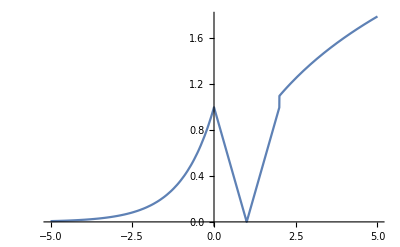

```mathematica
(*Question 4 a*)
f[x_]:=E^x/;x<0
f[x_]:=Abs[x-1]/;0≤x≤2
f[x_]:=Log[x+1]/;x>2
Plot[f[x],{x,-5,5}]
```

```mathematica
(*Range is [0,∞)*)
```

```mathematica
(*Question 4 b*)
fv=f[0]
l1=Limit[E^x,x->0,Direction->1]
l2=Limit[Abs[x-1],x->0,Direction->-1]
If[fv==l1==l2,Print["The function is continuous at x=0"],Print["the funtion is not continuous at x=0"]]
```

1

1

1

The function is continuous at x=0

```mathematica
(*Question 5 *)
Clear[p,c,f]
p=6 x^2-11 x y-10 y^2-19 y+c;
a=6;b=-10;
h=-11/2;g=0;f=-19/2;
Solve[Det[({{a, h, g}, {h, b, f}, {g, f, c}})]==0,c]
```

{{c→-6}}

(-2+2 x-5 y) (3+3 x+2 y)

-ArcTan[19/4]

X^2/16-Y^2/16==-(2 X Y)/11

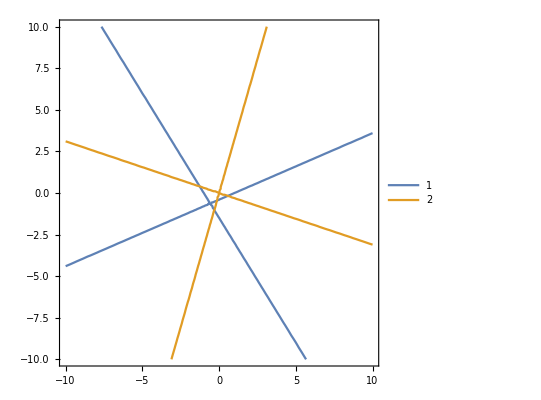

```mathematica
Factor[p/.c->-6]
ArcTan[(2 Sqrt[h^2-a b])/(a+b)]
Expand[(X^2-Y^2)/(a-b)==(X Y)/h]
ContourPlot[{(p/.c->-6)==0,(x^2-y^2)/(a-b)==(x y)/h},{x,-10,10},{y,-10,10},PlotLegends->Automatic]
```

```mathematica
(*Question 6 a*)
Solve[Sqrt[8 x]==x^3]
```

{{x→0},{x→2^(3/5)}}

```mathematica
Integrate[Sqrt[8 x]-x^3,{x,0,2^(3/5)}]//N
```

2.19918

```mathematica
(*Question 6 b*)
Clear[f]
f[x_]=x^4-12 x^3+48 x^2+12 x+1;
cri=NSolve[f'[x]==0,x]
inf=NSolve[f''[x]==0,x]
```

{{x→-0.119568},{x→4.55978-2.07335 ⅈ},{x→4.55978+2.07335 ⅈ}}

{{x→2.},{x→4.}}

```mathematica
{f'[-3],f'[3]}
```

{-708,84}

```mathematica
(*the function is increasing on (-0.11956761961144527,∞) and decreasing on (-∞,-0.11956761961144527)*)
```